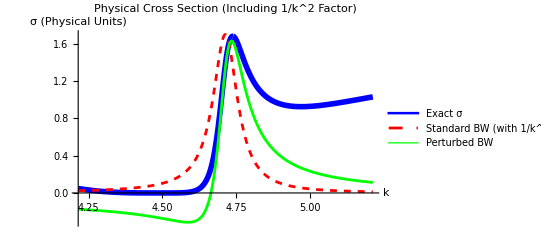

```mathematica
ClearAll["Global`*"]

(*1. Parameters*)
l=1;
μ=1;
a=1;
λ=20;

(*2. Define the Full Exact T-Matrix*)
(*From our earlier derivation:T=N/D*)
(*Note:We only need the k-dependence correct here.*)
(*The constants cancel when we normalize to the unitarity limit.*)
Num[k_]:=SphericalBesselJ[l,k*a]^2;
Denom[k_]:=1-I*k*λ*a^2*SphericalBesselJ[l,k*a]*SphericalHankelH1[l,k*a];

(*The "Unitary Limit" T-matrix at a pole is purely imaginary:i/(4 Pi^2 mu k)*)
(*So the physical scattering efficiency is|T/T_unitary|^2*)
(*This simplifies to:*)
ScatteringEfficiency[k_]:=Abs[(Num[k]/Denom[k])/(Num[k]/(I*Im[Denom[k]]))]^2;
(*Wait,simpler method:Just use Phase Shifts directly for exactness*)
(*T=e^(i d) sin(d).We need sin^2(d).*)
(*Argument of T gives the phase.*)
PhaseShift[k_]:=Arg[Num[k]/Denom[k]];
(*Careful with Arg ranges.Better to use Im[1/T] property or just the T magnitude*)

(*Let's stick to the Magnitude method which is robust:*)
(*Sigma=Prefactor* |T_normalized|^2*)
(*At resonance, |T_normalized| =1*)
ExactShape[k_]:=Abs[(-(I*k*λ*a^2)*Num[k])/Denom[k]]^2;
(*The term in Abs is exactly sin(delta)*e^i delta*)


(*3. Physical Pre-Factors*)
(*The geometric cross section limit*)
UnitaryLimit[k_]:=(4*Pi/k^2)*(2*l+1);


(*4. DEFINITIONS*)

(*A.Exact Physical Cross Section*)
SigmaExact[k_]:=UnitaryLimit[k]*ExactShape[k];

(*B.Find Pole*)
searchGuess=4.7-0.1 I;
root=FindRoot[Denom[k]==0,{k,searchGuess}];
kres=k/. root;

(*C.Standard Breit-Wigner (With 1/k^2)*)
(*We use the Energy-dependent Width form implicitly via the pole residue,*)
(*but keep the width Gamma fixed to the pole value.*)
(*We map E-plane variables to k-plane:*)
Γ=2*Abs[Im[kres]]*Re[kres]/μ; (*From E=k^2/2mu*)
E0=Re[kres]^2/(2*μ);
Energy[k_]:=k^2/(2*μ);

(*The Standard BW Formula in terms of E,but plotted vs k*)
SigmaBW[k_]:=UnitaryLimit[k]*(Γ^2/4)/((Energy[k]-E0)^2+Γ^2/4);


(*D.Perturbative Correction (The Shift)*)
(*We apply the correction to the SHAPE factor,not the 1/k^2 factor*)
Psi[k_]:=SphericalBesselJ[l,k*a];
SlopeS=(D[Psi[k],k]/. k->kres)/Psi[kres];

(*Note:The correction allows the width to "run"*)
SigmaPerturbative[k_]:=SigmaBW[k]*(1+4*Re[(k-kres)*SlopeS]);


(*5. Plotting*)
Plot[{SigmaExact[k],SigmaBW[k],SigmaPerturbative[k]},{k,Re[kres]-0.5,Re[kres]+0.5},PlotStyle->{{Blue,Thickness[0.01]},{Red,Dashed},{Green,Thickness[0.005]}},PlotLegends->{"Exact σ","Standard BW (with 1/k^2)","Perturbed BW"},AxesLabel->{"k","σ (Physical Units)"},PlotLabel->"Physical Cross Section (Including 1/k^2 Factor)"]
```